→ Exercício 1

Defino T_0 como sendo o período clássico do problema de pequenas oscilações e T como sendo o período do problema genérico em estudo. Incluo a função "NIntegrate" para obter uma aproximação numérica da integral que fornece o período completo T

```mathematica
Subscript[T, 0]:=2π √(l/g);
T[θ0_]:=√((8l)/g)NIntegrate[1/(√(Cos[θ]-Cos[θ0])),{θ,0,θ0 }];
```

NIntegrate::inumri: The integrand 1/(√(-1.+Cos[θ])) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.0000635365,0.00006353646620935395666506259646696241332679183145583368119702072363}}.

NIntegrate::inumri: The integrand 1./(√(-1.+Cos[θ])) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.0000635365,0.00006353646620935395666506259646696241332679183145583368119702072363}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

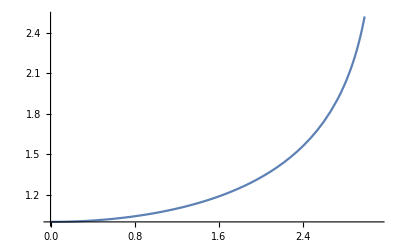

```mathematica
Plot[T[θ0]/Subscript[T, 0],{θ0,0,.99π}]
```

Para evitar os problemas de “overflow” obtidos para ângulos θ próximos de θ_0 =0, redefino o limite superior da integral para que a integração seja finalizada em um valor de ângulo diferente de minimamente diferente de θ_0.

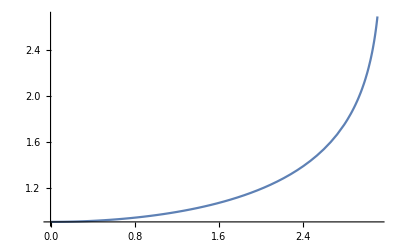

```mathematica
T[θ0_]:=√((8l)/g)NIntegrate[1/(√(Cos[θ]-Cos[θ0])),{θ,0,.99θ0 }]; 
Plot[T[θ0]/Subscript[T, 0],{θ0,0,.99π}]
```

→ Exercício 2
Construo as equações considerando a seguinte distribuição de correntes no circuito:

-Graphics-

Ou seja, i1 é a corrente que passa na resistência R_1, i2 na resistência R_6, i3 na resistência R_3, i4 em R_2, i5 em R_5 e i6 em R_4.Defino as equações obtidas por meio das Leis de Kirchoff e aplico a função “Solve” para obter as soluções das correntes. Em seguida, aplico a função “ReplaceAll” para identificar os valores numéricos com base nas constantes fornecidas no enunciado do exercício.

```mathematica
eq1=E1-i1 R1-i3 R3-i4 R2 ==0;  
eq2=-i2 R6 + E2+i6 R4+i3 R3==0;
eq3=-i6 R4 - i5 R5 +i4 R2==0;
eq4=i1==i2+i3;
eq5=i2+i6==i5;
eq6=i3==i4+i6;
eq7=i4+i5==i1;
eqs={eq1,eq2,eq3,eq4,eq5,eq6,eq7};
correntes={i1,i2,i3,i4,i5,i6};

Solve[eqs,correntes]
ReplaceAll[%,{E1-> 12,E2->8,R1->20,R2->15,R3->3,R4->6,R5->12,R6->2}]
```

{{i1→-((-E1 R2 R3-E2 R2 R3-E1 R2 R4-E2 R2 R4-E1 R3 R4-E2 R3 R4-E1 R3 R5-E2 R3 R5-E1 R4 R5-E1 R2 R6-E1 R4 R6-E1 R5 R6)/(R1 R2 R3+R1 R2 R4+R1 R3 R4+R1 R3 R5+R2 R3 R5+R1 R4 R5+R2 R4 R5+R3 R4 R5+R1 R2 R6+R2 R3 R6+R1 R4 R6+R2 R4 R6+R3 R4 R6+R1 R5 R6+R2 R5 R6+R3 R5 R6)),i2→-((-E2 R1 R2-E1 R2 R3-E2 R2 R3-E2 R1 R4-E1 R2 R4-E2 R2 R4-E1 R3 R4-E2 R3 R4-E2 R1 R5-E2 R2 R5-E1 R3 R5-E2 R3 R5)/(R1 R2 R3+R1 R2 R4+R1 R3 R4+R1 R3 R5+R2 R3 R5+R1 R4 R5+R2 R4 R5+R3 R4 R5+R1 R2 R6+R2 R3 R6+R1 R4 R6+R2 R4 R6+R3 R4 R6+R1 R5 R6+R2 R5 R6+R3 R5 R6)),i3→-((-(-R1 R4+R1 (-R2-R5)-R2 R5) (E2 R1-E1 R6)+E1 R5 (-R1 R4+R2 R6))/((R1 R4-R3 R5) (-R1 R4+R2 R6)-(-R1 R4+R1 (-R2-R5)-R2 R5) (R1 R4+R3 R6+R1 (R3+R6)))),i4→-((E2 R1 R4-E1 R3 R5-E2 R3 R5-E1 R4 R5-E1 R4 R6-E1 R5 R6)/(R1 R2 R3+R1 R2 R4+R1 R3 R4+R1 R3 R5+R2 R3 R5+R1 R4 R5+R2 R4 R5+R3 R4 R5+R1 R2 R6+R2 R3 R6+R1 R4 R6+R2 R4 R6+R3 R4 R6+R1 R5 R6+R2 R5 R6+R3 R5 R6)),i5→-((-E1 R2 R3-E2 R2 R3-E2 R1 R4-E1 R2 R4-E2 R2 R4-E1 R3 R4-E2 R3 R4-E1 R2 R6)/(R1 R2 R3+R1 R2 R4+R1 R3 R4+R1 R3 R5+R2 R3 R5+R1 R4 R5+R2 R4 R5+R3 R4 R5+R1 R2 R6+R2 R3 R6+R1 R4 R6+R2 R4 R6+R3 R4 R6+R1 R5 R6+R2 R5 R6+R3 R5 R6)),i6→-((E2 R1 R2+E2 R1 R5+E2 R2 R5+E1 R3 R5+E2 R3 R5-E1 R2 R6)/(R1 R2 R3+R1 R2 R4+R1 R3 R4+R1 R3 R5+R2 R3 R5+R1 R4 R5+R2 R4 R5+R3 R4 R5+R1 R2 R6+R2 R3 R6+R1 R4 R6+R2 R4 R6+R3 R4 R6+R1 R5 R6+R2 R5 R6+R3 R5 R6))}}

{{i1→906/1519,i2→250/217,i3→-844/1519,i4→176/1519,i5→730/1519,i6→-1020/1519}}

→ Exercício 3
Aplico a definição de reta tangente e efetuo os cálculos considerando a função de derivada total “Dt” e a função “Solve”

```mathematica
eq=(x/a)^3+(y/b)^3==(6x y)/(a b);
SetAttributes[{a,b},Constant];
```

```mathematica
Simplify[y-y0==m(x-x0)/.{m->Dt[y,x]/.First[Solve[Dt[eq,x],Dt[y,x]]]/.{x->x0, y->y0}}/.{x0->3a,y0->3b}]
```

b (6-x/a)==y